```mathematica
(*Define function to find 'x' where H=0 at the toe for given α,f,b0*)
xPosRoot[αv_?NumericQ,fv_?NumericQ, b0_?NumericQ,k_?NumericQ]:=Module[{sol,res},sol=Quiet@Check[NDSolve[{-D[H[x],x] - 0.5*(αv-2 b0 x)/(1+(2 b0 x)^2)*2 b0/(1+2 b0 x*αv)*H[x] == fv+2 b0 x -(αv-2 b0 x)/(1+2 b0 x*αv),H[0]==k*Abs[b0]},H,{x,0,1}],$Failed];
If[sol===$Failed,1.0,(*fallback if solve fails*)
Quiet@Check[res=x/.Last[FindRoot[((H[x]/. sol)==0),{x,0.9,0,1}]],0]
]
]
(*Define function to find 'x' where H=0 at the head for given α,f,b0*)
xNegRoot[αv_?NumericQ,fv_?NumericQ, b0_?NumericQ,k_?NumericQ]:=Module[{sol,res},sol=Quiet@Check[NDSolve[{-D[H[x],x] - 0.5*(αv-2 b0 x)/(1+(2 b0 x)^2)*2 b0/(1+2 b0 x*αv)*H[x] == fv+2 b0 x -(αv-2 b0 x)/(1+2 b0 x*αv),H[0]==k*Abs[b0]},H,{x,-1,0}],$Failed];
If[sol===$Failed,-1.0,(*fallback if solve fails*)
Quiet@Check[res=x/.Last[FindRoot[((H[x]/. sol)==0),{x,-0.9,-1,0}]],0]
]
]
(*Define functions to compute locus of stability*)
locusPosFun[f_?NumericQ,b0_?NumericQ,k_?NumericQ]:=Module[{res},res=
Quiet@FindRoot[xPosRoot[αsol,f,b0,k]==0.99,{αsol,0.0,0,10}];
αsol/. res]
locusNegFun[f_,b0_,k_]:=Module[{res},res=
Quiet@FindRoot[xNegRoot[αsol,f,b0,k]==-0.99,{αsol,1.2,0,10}];
αsol/. res]
(*bvals=Subdivide[0.1,0.4,3];*)
bvals={0.1,0.2,0.3,0.4};
roundedLabels = Round[bvals,0.01];
fvals=Range[0,1,0.01];  

bestα[b0_,k_] := Sqrt[(k*b0 - 2*b0)/b0/(2+k/2*b0^2)]
bestf[b0_,k_] := bestα[b0,k]*(1-k*b0^2)

(*Parallel computation of {f,alpha} pairs for each ρ,b value*)
kval=0.5;
dataPos=ParallelTable[{f,locusPosFun[f,b,kval]-(2-kval)*b},{b,bvals},{f,fvals}];
kval=1.0;
dataPos2=ParallelTable[{f,locusPosFun[f,b,kval]-(2-kval)*b},{b,bvals},{f,fvals}];
kval=1.5;
dataPos3=ParallelTable[{f,locusPosFun[f,b,kval]-(2-kval)*b},{b,bvals},{f,fvals}];
(*dataNeg=ParallelTable[{f,locusNegFun[f,b,kval]+(2-kval)*b},{b,bvals},{f,fvals}];*)
(*Plot each set of points as a line*)
styles=Table[{ColorData["ThermometerColors"][r],Thick},{r,Rescale[Range[Length[bvals]]]}];
styles2=Table[{ColorData["ThermometerColors"][r],Thickness[0.002]},{r,Rescale[Range[Length[bvals]]]}];
styles3=Table[{ColorData["ThermometerColors"][r],Dashed},{r,Rescale[Range[Length[bvals]]]}];
```

## Plot results

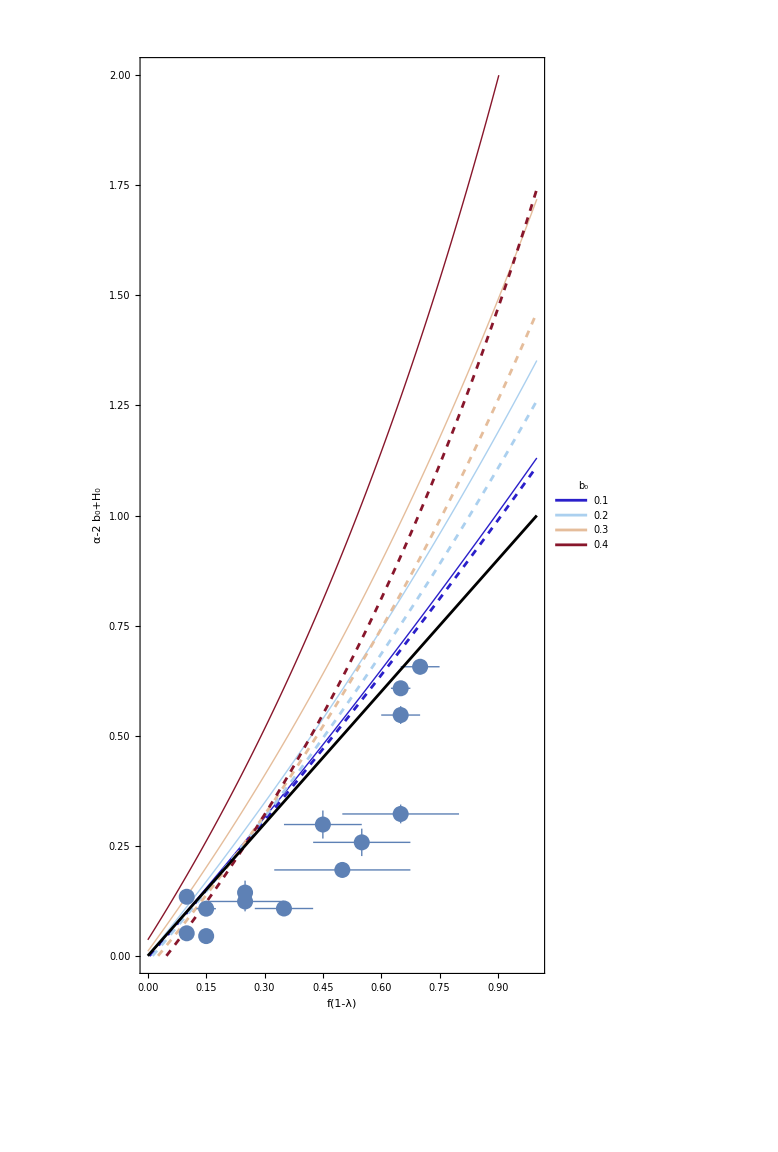

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeNormalizedStabilityBoundaryPlot.jpg

```mathematica
p1=ListLinePlot[dataPos,PlotRange->{0,2},
PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,20]],Right],
LabelStyle->{FontSize->20},
ImageSize->Large,PlotStyle->styles];
p2=ListLinePlot[dataPos2,PlotRange->{0,2},
ImageSize->Large,
PlotStyle->styles2];
p3=ListLinePlot[dataPos3,PlotRange->{0,2},
ImageSize->Large,
PlotStyle->styles3];
p4=Plot[f,{f,0,1},PlotStyle->{Black}];

(*Read file with Landslide data*)
data=Import[NotebookDirectory[]<>"ResultsLandslideDatabase.csv","CSV"];
pts=Rest[data];
pointsWithErrors=pts/. {f_,α_,Δf_,Δα_}:>{Around[f,Δf],Around[α,Δα]};

p5=ListPlot[pointsWithErrors,PlotStyle->{DarkBlue,PointSize[0.02]}];

fig=Show[p1,p3,p5,p4,FrameLabel->{Style["f(1-λ)",25],Style["α"+Subscript["H",0]-2 Subscript["b",0],25]},Frame->True,LabelStyle->{FontSize->25},AspectRatio->2,PlotRange->{0,2}]
Export[NotebookDirectory[]<>"LandslideToeNormalizedStabilityBoundaryPlot.jpg",fig,"JPEG"]
```

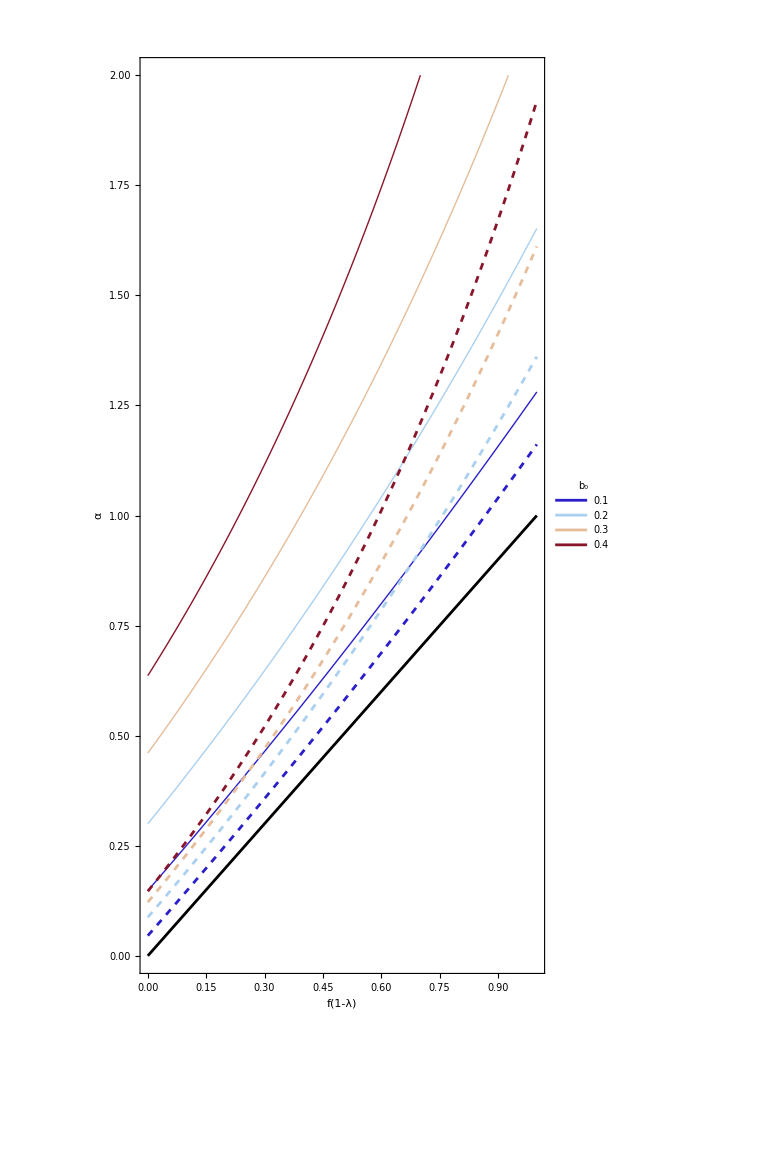

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/LandslideToeStabilityBoundaryPlot.jpg

```mathematica
(*Parallel computation of {f,alpha} pairs for each ρ,b value*)
kval=0.5;
dataPos=ParallelTable[{f,locusPosFun[f,b,kval]},{b,bvals},{f,fvals}];
kval=1.5;
dataPos2=ParallelTable[{f,locusPosFun[f,b,kval]},{b,bvals},{f,fvals}];
p1=ListLinePlot[dataPos,PlotRange->{0,2},
PlotLegends->Placed[LineLegend[roundedLabels,LegendLabel->Style["b₀",Bold,20]],Right],
LabelStyle->{FontSize->20},
ImageSize->Large,PlotStyle->styles];
p2=ListLinePlot[dataPos2,PlotRange->{0,2},
ImageSize->Large,
PlotStyle->styles3];

fig=Show[p1,p2,p4,FrameLabel->{Style["f(1-λ)",25],Style["α",25]},Frame->True,LabelStyle->{FontSize->25},AspectRatio->2,PlotRange->{0,2}]
Export[NotebookDirectory[]<>"LandslideToeStabilityBoundaryPlot.jpg",fig,"JPEG"]
```